```mathematica
Integrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(4-4Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{r>0}]
```

$Aborted

```mathematica
FullSimplify[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(4-4Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ]]
```

Sin[θ]/(4 π (1/8+(-2+w+2 Cos[Cos[ϕ] Sin[θ]])^2))

```mathematica
FullSimplify[(-32Cos[x]+16+16 Cos[x]^2)^(1/2)]
```

4 √((-1+Cos[x])^2)

```mathematica
(((1.913*2.818)^2)*1.0/(2*π*1.0))*2
```

9.25043

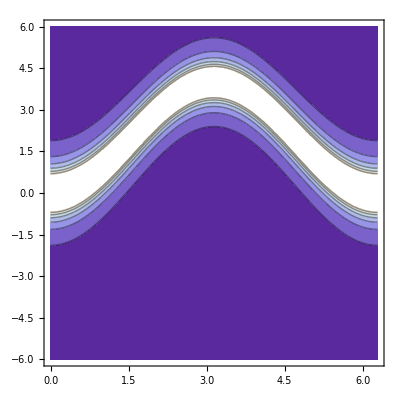

```mathematica
ContourPlot[2*(((1.913*2.818)^2)*1.0/(2*π*1.0))((14.7-(4-4Cos[kx]))/14.7)1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(4-4Cos[kx]))^2),{kx,0,2π},{w,-6,6}]
```

```mathematica
(Exp[(4-4Cos[1])/(8.617343*10^-2*0.0001)]-1)^-1
```

3.665606056×10^-46336

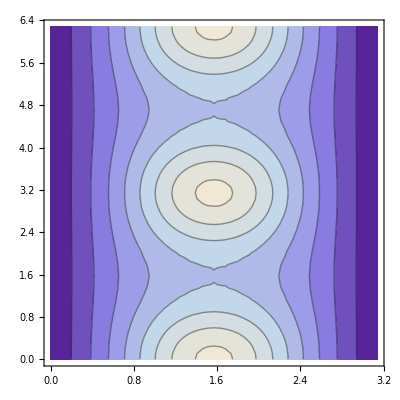

```mathematica
ContourPlot[1/π(1/2(1/2))/((1/2(1/2)^2)+(4-(4-4Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
NIntegrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(0-(4-4Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

5.04313

```mathematica
2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(4-4Cos[kx]))/14.7)*
```

9.25043

```mathematica
vals=Table[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(4-4Cos[kx]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(4-4Cos[kx]))^2),{w,0,5,.2},{kx,0,π,.2}];
```

```mathematica
2*4/π//N
```

2.54648

```mathematica
Max[vals]
```

23.556

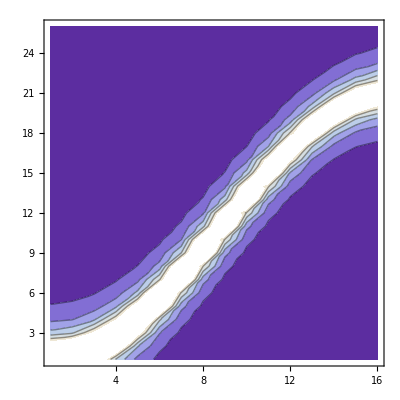

```mathematica
ListContourPlot[vals]
```

```mathematica
(1/(Exp[(4-4Cos[r Sin[θ]Cos[ϕ]])/((8.617343*10^-2)*0.001)]-1))/.{r->1,θ->0.0001,ϕ->0}//N
```

8616.84

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))(1/(Exp[(4-4Cos[r Sin[θ]Cos[ϕ]])/((8.617343*10^-2)*0.001)]-1)+1)((14.7-(4-4Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(4-4Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"Trapezoidal"}],{r,0.1,π,π/30},{w,0,5,1/6}]//Quiet
```

{{2.821,1.97898,1.02974,0.570791,0.351148,0.234817,0.167099,0.124606,0.0963286,0.0766169,0.0623529,0.0517102,0.0435648,0.0371953,0.0321224,0.0280178,0.0246503,0.021854,0.0195069,0.0175179,0.0158177,0.0143532,0.0130827,0.0119735,0.0109995,0.0101395,0.00937651,0.0086964,0.00808762,0.00754055,0.00704712},{11.4175,8.3975,4.38815,2.41409,1.47481,0.98107,0.695437,0.517065,0.398814,0.316629,0.257301,0.213123,0.179368,0.153009,0.132042,0.115094,0.101203,0.0896773,0.0800099,0.0718225,0.0648283,0.0588066,0.0535853,0.0490289,0.0450291,0.041499,0.0383679,0.0355779,0.0330812,0.0308382,0.0288157},{25.4115,20.3993,10.8411,5.88965,3.55227,2.34036,1.64728,1.21829,0.935836,0.74059,0.600256,0.496129,0.416802,0.355012,0.305965,0.266392,0.234008,0.207177,0.184699,0.165684,0.149456,0.135497,0.123403,0.112857,0.103606,0.0954457,0.0882122,0.0817701,0.0760082,0.070834,0.0661703},{43.0502,39.0194,21.8524,11.7003,6.91419,4.48473,3.12105,2.28903,1.7472,1.37584,1.11072,0.915073,0.766696,0.651557,0.560453,0.487151,0.427308,0.377828,0.336453,0.301509,0.27173,0.246149,0.224012,0.204729,0.18783,0.172938,0.159748,0.14801,0.137519,0.128104,0.119623},{61.908,63.201,39.8403,21.3422,12.2468,7.75262,5.30173,3.83951,2.90319,2.26964,1.82186,1.49406,1.24707,1.05644,0.906282,0.785934,0.688011,0.607278,0.539942,0.483199,0.434942,0.39356,0.357808,0.326711,0.299495,0.275541,0.254347,0.235506,0.218682,0.203598,0.190021},{80.2467,88.8103,65.8985,37.7831,21.0299,12.8306,8.54025,6.06765,4.52467,3.50059,2.78736,2.27123,1.88592,1.59076,1.35974,1.17555,1.02635,0.90383,0.801986,0.71642,0.643841,0.581751,0.528222,0.481751,0.44115,0.405472,0.373951,0.345966,0.321008,0.298655,0.278558},{97.4447,112.643,94.6967,64.1795,36.5096,21.2346,13.552,9.34754,6.82657,5.20176,4.09466,3.3068,2.7263,2.28631,1.94487,1.6746,1.45701,1.27925,1.13214,1.00903,0.904971,0.816217,0.73991,0.673826,0.616217,0.565693,0.521138,0.481648,0.446483,0.415033,0.386793},{113.501,134.118,120.601,95.0766,63.3373,36.5224,21.9656,14.4563,10.2201,7.61155,5.89234,4.69882,3.83598,3.19164,2.69758,2.31032,2.00107,1.75016,1.54375,1.37188,1.22725,1.10438,0.999105,0.908217,0.829205,0.760084,0.699268,0.645477,0.597667,0.554984,0.516718},{128.571,153.863,143.474,122.068,96.2239,64.4794,37.803,23.2248,15.5818,11.1951,8.45044,6.61571,5.32606,4.38348,3.67281,3.12326,2.68925,2.34034,2.05553,1.81997,1.62287,1.45626,1.31414,1.19191,1.08603,0.993695,0.91268,0.841206,0.777828,0.721365,0.670846},{142.766,172.767,163.728,143.938,123.242,99.3033,67.7627,40.3612,25.0559,16.9746,12.3088,9.36934,7.39017,5.98906,4.95809,4.1759,3.56752,3.0845,2.6943,2.37436,2.10865,1.88549,1.69619,1.5342,1.39448,1.2731,1.16697,1.07364,0.991115,0.917784,0.852328},{156.133,191.398,179.478,162.933,144.384,123.691,104.273,73.1425,44.4666,27.6462,18.6949,13.6004,10.3947,8.23386,6.70046,5.5687,4.70719,4.03485,3.49926,3.0652,2.70821,2.41087,2.16046,1.9475,1.76481,1.60688,1.46939,1.34894,1.2428,1.14879,1.06511},{168.688,209.792,196.54,180.806,166.122,144.033,127.016,110.817,80.7963,50.0488,30.9512,20.8207,15.115,11.5545,9.16521,7.47285,6.22414,5.27297,4.52976,3.93681,3.45543,3.05881,2.72787,2.44865,2.21077,2.00637,1.82936,1.67503,1.53961,1.42012,1.31413},{180.453,227.547,214.605,198.564,178.014,167.787,147.927,131.345,118.528,89.7864,57.4876,35.2694,23.5215,16.9039,12.8785,10.2029,8.3186,6.93291,5.87925,5.05657,4.40026,3.86726,3.42782,3.06084,2.75092,2.48662,2.25927,2.06219,1.89016,1.73906,1.60558},{191.471,244.194,234.673,214.363,194.819,177.941,168.776,151.501,136.3,126.941,99.8343,66.9062,40.8442,26.7693,19.085,14.3973,11.3649,9.24916,7.70264,6.53129,5.61899,4.89228,4.3026,3.81661,3.41077,3.06797,2.77552,2.52383,2.30553,2.11486,1.94728},{201.792,259.557,256.259,220.875,212.489,190.87,190.804,169.651,155.995,141.647,135.61,110.431,78.1287,47.9188,30.7664,21.5917,16.1394,12.667,10.2739,8.53924,7.23298,6.21963,5.41465,4.76267,4.22602,3.77821,3.40013,3.07765,2.80013,2.55938,2.34907},{211.464,273.816,277.154,238.602,226.268,209.253,189.506,196.091,170.962,161.235,147.286,144.225,121.28,90.6025,56.6423,35.6287,24.5349,18.1793,14.1191,11.3979,9.44552,7.98587,6.85937,5.96781,5.24765,4.65602,4.16303,3.7472,3.39276,3.08785,2.82343},{220.518,287.33,295.186,262.36,236.266,227.039,204.692,191.859,200.885,173.015,167.123,153.22,152.736,132.281,103.593,66.935,41.4131,27.9351,20.413,15.7208,12.6193,10.4194,8.78802,7.53644,6.55022,5.75617,5.10542,4.56414,4.1082,3.71996,3.38621},{228.971,300.446,309.783,289.8,236.555,238.089,225.901,201.034,197.325,205.452,175.933,173.643,159.531,161.349,143.409,116.548,78.3962,48.048,31.7564,22.8699,17.5037,13.9257,11.4517,9.63258,8.2456,7.15773,6.28489,5.57147,4.97926,4.48119,4.05757},{236.823,313.412,321.916,315.119,258.802,243.94,242.242,211.128,200.078,204.862,210.051,179.764,180.86,166.391,170.418,154.68,129.279,90.3569,55.2605,35.8728,25.4811,19.3272,15.29,12.5242,10.5065,8.97722,7.78301,6.82808,6.04958,5.40464,4.86306},{244.066,326.352,333.044,349.88,291.268,250.288,249.384,244.472,218.292,202.629,213.75,214.848,184.543,188.924,174.078,180.336,166.238,141.85,102.051,62.5377,40.0419,28.1224,21.1704,16.7163,13.608,11.3898,9.71677,8.41518,7.37735,6.53314,5.83497},{250.685,339.285,344.254,360.29,326.583,252.818,251.148,257.042,243.951,214.799,208.608,244.959,219.936,190.337,198.078,182.992,191.502,190.166,154.344,112.718,69.1547,43.907,30.6158,22.9347,18.0502,14.6641,12.2557,10.445,9.03991,7.92175,7.01356},{256.668,352.133,356.048,362.871,384.848,287.731,254.076,259.409,263.234,223.91,213.139,217.499,254.445,225.383,197.274,208.667,193.684,204.374,204.433,166.686,121.504,74.27,47.0468,32.7503,24.5031,19.2677,15.6463,13.0721,11.139,9.64016,8.44822},{262.008,364.736,368.607,361.239,405.049,331.891,247.44,257.684,270.406,266.977,226.899,214.383,228.763,264.345,231.284,212.301,221.174,206.879,219.542,219.727,178.439,127.218,77.0852,49.0737,34.3248,25.7602,20.2456,16.5066,13.8058,11.7744,10.1976},{266.706,376.882,382.104,358.085,410.575,372.285,283.79,258.192,267.768,280.476,237.821,236.539,219.349,242.087,274.783,237.847,224.528,236.27,223.517,237.834,222.448,188.322,128.244,77.0848,49.7531,35.2002,26.6168,21.0252,17.2032,14.426,12.3282},{270.771,388.337,396.796,354.671,407.084,443.866,334.915,243.717,263.87,281.748,288.81,241.16,234.957,228.527,257.479,285.689,245.518,239.737,254.865,244.78,260.316,239.324,193.134,123.168,74.3032,49.0851,35.3374,26.973,21.5208,17.7069,14.9097},{274.224,398.883,412.894,351.016,400.063,456.307,386.591,281.834,262.639,274.793,295.816,295.226,246.617,235.302,242.151,275.243,296.82,255.169,258.934,278.097,272.087,287.684,253.957,187.049,112.281,69.3958,47.2985,34.8024,26.9568,21.7259,18.006},{277.092,408.34,430.379,346.669,393.039,452.798,477.681,338.797,242.188,270.405,290.835,308.186,258.074,267.458,239.223,260.269,328.163,307.927,268.294,283.715,307.176,307.19,317.147,257.579,166.143,98.2052,63.3565,44.6863,33.679,26.5672,21.6619},{279.411,416.584,448.928,405.01,387.872,441.97,499.949,400.441,282.931,267.415,281.745,309.286,319.673,264.252,267.966,248.624,282.888,346.579,319.311,287.148,316.967,314.066,351.88,335.306,233.612,136.75,84.0824,57.0334,41.7671,32.2593,25.8862},{281.221,423.545,467.96,417.097,384.481,429.719,498.951,447.603,345.378,243.3,277.872,298.434,326.422,330.102,273.473,269.626,265.447,310.377,367.611,333.051,326.178,363.681,375.413,399.06,309.706,184.504,109.374,71.7043,51.1496,38.7461,30.6368},{282.566,429.206,486.76,431.659,380.905,418.987,485.039,541.584,415.882,287.558,272.574,290.324,320.661,342.091,285.697,285.671,274.922,291.512,344.114,391.133,354.907,378.99,394.247,453.035,397.606,239.121,138.51,88.2278,61.5656,45.8716,35.8145}}

# ← This is what the plot looks like with the proper form factor: (1/2 g F(κ))^2

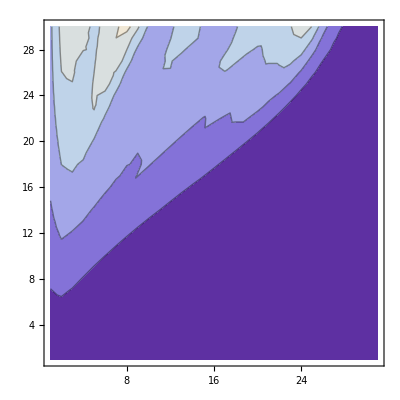

```mathematica
ListContourPlot[lst]
```

```mathematica
{523.344637790916,555.9775801528555,450.06826127053,382.71046461343843,347.73005630451695,325.8338326661845,315.42654257661275,308.86972242582453,316.8065973058143,325.9091444272565,367.1680606203278,425.17102547928755,389.53220933181194,138.88782240241227,62.103054915446,36.40288824724365}-{467.069221453134,519.808010478993,292.322299510204,287.244284529843,338.980954219716,379.727324543641,162.435417988404,36.4186853770459,618.010974246558,315.216512739039,312.100549953185,301.621675124277,394.876533038488,434.581085996050,65.3287841142702,0}
```

{56.2754,36.1696,157.746,95.4662,8.7491,-53.8935,152.991,272.451,-301.204,10.6926,55.0675,123.549,-5.34432,-295.693,-3.22573,36.4029}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(4-4Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(0-(4-4Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{r,0,π,π/15}]//Quiet
```

{0.,12.6457,47.5919,91.2251,130.152,167.776,200.727,236.014,275.789,313.843,343.02,383.371,410.599,448.831,495.554,521.856}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(4-4Cos[π Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(4-4Cos[π Sin[θ]Cos[ϕ]]))^2)π^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{w,0,5,1/3}]//Quiet
```

{523.345,555.978,450.068,382.71,347.73,325.834,315.427,308.87,316.807,325.909,367.168,425.171,389.532,138.888,62.1031,36.4029}

```mathematica
((1.913*2.818^2)*1.0/(2*π*1.0))((14.7-(4-4Cos[r Sin[θ]Cos[ϕ]]))/14.7)
```

2.41778

```mathematica
y[x_]:=√((0.0706*Exp[-35.008*x^2]+0.3589*Exp[-15.358*x^2]+0.5819*Exp[-5.561*x^2]-0.0114)^2)
```

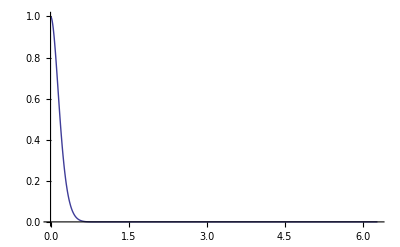

```mathematica
Plot[y[x]^2,{x,0,2π},PlotRange->All]
```

```mathematica
Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))(1/(Exp[(4-4Cos[r Sin[θ]Cos[ϕ]])/((8.617343*10^-2)*0.001)]-1)+1)((14.7-(4-4Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"Trapezoidal"}],{r,0.1,π,π/30},{w,0,5,1/6}]//Quiet
```

```mathematica
N[Table[(1/(Exp[Abs[(4-4Cos[r Sin[θ]Cos[ϕ]])]/((8.617343*10^-2)*0.001)]-1)),{θ,0.001,π},{ϕ,0,2π}],3]/.r->1//TableForm
```

85.6744 | 294.689 | 497.1 | 87.4254 | 201.194 | 1070.45 | 92.9719
1.1752145583×10^-3367 | 6.0448879357×10^-1026 | 3.31684544422×10^-613 | 1.55185086111×10^-3304 | 3.45023051553×10^-1489 | 7.18927×10^-287 | 2.6259245475×10^-3119
4.31760086406×10^-3885 | 7.69101320994×10^-1192 | 3.82582492637×10^-713 | 4.97165346711×10^-3813 | 9.6782124083×10^-1728 | 7.321439991843×10^-334 | 2.1884401311×10^-3601
1.58066×10^-99 | 1.33005×10^-29 | 7.35569×10^-18 | 1.45644×10^-97 | 5.59261×10^-43 | 1.09161×10^-8 | 7.95979×10^-92

```mathematica
Table[Abs[1Sin[θ]Cos[ϕ]],{θ,0.001,π},{ϕ,0,2π}]//TableForm
```

0.001 | 0.000540302 | 0.000416147 | 0.000989992 | 0.000653644 | 0.000283662 | 0.00096017
0.842011 | 0.45494 | 0.3504 | 0.833584 | 0.550375 | 0.238847 | 0.808474
0.908881 | 0.49107 | 0.378228 | 0.899785 | 0.594084 | 0.257815 | 0.87268
0.14013 | 0.0757125 | 0.0583146 | 0.138728 | 0.091595 | 0.0397496 | 0.134549

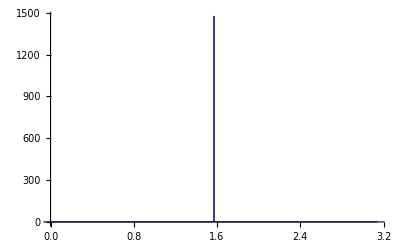

```mathematica
Plot[((1/(Exp[Abs[(4-4Cos[r Sin[θ]Cos[ϕ]])]/((8.617343*10^-2)*0.001)]-1))/.{r->1,θ->π/2}),{ϕ,0,π}]
```

```mathematica
((1/(Exp[Abs[(4-4Cos[r Sin[θ]Cos[ϕ]])]/((8.617343*10^-2)*0.001)]-1))/.ϕ->0)
```

1/(-1+ⅇ^(11604.5 Abs[4-4 Cos[r Sin[θ]]]))

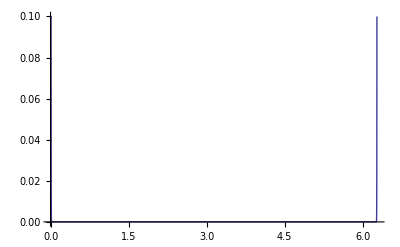

```mathematica
Plot[(1/(Exp[Abs[(4-4Cos[kx])]/((8.617343*10^-2)*0.001)]-1)),{kx,0,2*π},PlotRange->{0,0.1}]
```

```mathematica
(1/(Exp[Abs[(4-4Cos[kx])]/((8.617343*10^-2)*0.001)]-1))/.kx->0.0001
```

4308.17

```mathematica
Reduce[4-4Cos[r Sin[θ]Cos[ϕ]]==0]
```

Cos[r Cos[ϕ] Sin[θ]]==1

```mathematica
Reduce[r Cos[ϕ]Sin[θ]==0]
```

r==0||Cos[ϕ]==0||Sin[θ]==0

```mathematica
Table[N[Abs[Cos[ϕ]Sin[θ]],2],{θ,0,π,π/20},{ϕ,0,2π,2π/20}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.16 | 0.15 | 0.13 | 0.092 | 0.048 | 0 | 0.048 | 0.092 | 0.13 | 0.15 | 0.16 | 0.15 | 0.13 | 0.092 | 0.048 | 0 | 0.048 | 0.092 | 0.13 | 0.15 | 0.16
0.31 | 0.29 | 0.25 | 0.18 | 0.095 | 0 | 0.095 | 0.18 | 0.25 | 0.29 | 0.31 | 0.29 | 0.25 | 0.18 | 0.095 | 0 | 0.095 | 0.18 | 0.25 | 0.29 | 0.31
0.45 | 0.43 | 0.37 | 0.27 | 0.14 | 0 | 0.14 | 0.27 | 0.37 | 0.43 | 0.45 | 0.43 | 0.37 | 0.27 | 0.14 | 0 | 0.14 | 0.27 | 0.37 | 0.43 | 0.45
0.59 | 0.56 | 0.48 | 0.35 | 0.18 | 0 | 0.18 | 0.35 | 0.48 | 0.56 | 0.59 | 0.56 | 0.48 | 0.35 | 0.18 | 0 | 0.18 | 0.35 | 0.48 | 0.56 | 0.59
0.71 | 0.67 | 0.57 | 0.42 | 0.22 | 0 | 0.22 | 0.42 | 0.57 | 0.67 | 0.71 | 0.67 | 0.57 | 0.42 | 0.22 | 0 | 0.22 | 0.42 | 0.57 | 0.67 | 0.71
0.81 | 0.77 | 0.65 | 0.48 | 0.25 | 0 | 0.25 | 0.48 | 0.65 | 0.77 | 0.81 | 0.77 | 0.65 | 0.48 | 0.25 | 0 | 0.25 | 0.48 | 0.65 | 0.77 | 0.81
0.89 | 0.85 | 0.72 | 0.52 | 0.28 | 0 | 0.28 | 0.52 | 0.72 | 0.85 | 0.89 | 0.85 | 0.72 | 0.52 | 0.28 | 0 | 0.28 | 0.52 | 0.72 | 0.85 | 0.89
0.95 | 0.9 | 0.77 | 0.56 | 0.29 | 0 | 0.29 | 0.56 | 0.77 | 0.9 | 0.95 | 0.9 | 0.77 | 0.56 | 0.29 | 0 | 0.29 | 0.56 | 0.77 | 0.9 | 0.95
0.99 | 0.94 | 0.8 | 0.58 | 0.31 | 0 | 0.31 | 0.58 | 0.8 | 0.94 | 0.99 | 0.94 | 0.8 | 0.58 | 0.31 | 0 | 0.31 | 0.58 | 0.8 | 0.94 | 0.99
1. | 0.95 | 0.81 | 0.59 | 0.31 | 0 | 0.31 | 0.59 | 0.81 | 0.95 | 1. | 0.95 | 0.81 | 0.59 | 0.31 | 0 | 0.31 | 0.59 | 0.81 | 0.95 | 1.
0.99 | 0.94 | 0.8 | 0.58 | 0.31 | 0 | 0.31 | 0.58 | 0.8 | 0.94 | 0.99 | 0.94 | 0.8 | 0.58 | 0.31 | 0 | 0.31 | 0.58 | 0.8 | 0.94 | 0.99
0.95 | 0.9 | 0.77 | 0.56 | 0.29 | 0 | 0.29 | 0.56 | 0.77 | 0.9 | 0.95 | 0.9 | 0.77 | 0.56 | 0.29 | 0 | 0.29 | 0.56 | 0.77 | 0.9 | 0.95
0.89 | 0.85 | 0.72 | 0.52 | 0.28 | 0 | 0.28 | 0.52 | 0.72 | 0.85 | 0.89 | 0.85 | 0.72 | 0.52 | 0.28 | 0 | 0.28 | 0.52 | 0.72 | 0.85 | 0.89
0.81 | 0.77 | 0.65 | 0.48 | 0.25 | 0 | 0.25 | 0.48 | 0.65 | 0.77 | 0.81 | 0.77 | 0.65 | 0.48 | 0.25 | 0 | 0.25 | 0.48 | 0.65 | 0.77 | 0.81
0.71 | 0.67 | 0.57 | 0.42 | 0.22 | 0 | 0.22 | 0.42 | 0.57 | 0.67 | 0.71 | 0.67 | 0.57 | 0.42 | 0.22 | 0 | 0.22 | 0.42 | 0.57 | 0.67 | 0.71
0.59 | 0.56 | 0.48 | 0.35 | 0.18 | 0 | 0.18 | 0.35 | 0.48 | 0.56 | 0.59 | 0.56 | 0.48 | 0.35 | 0.18 | 0 | 0.18 | 0.35 | 0.48 | 0.56 | 0.59
0.45 | 0.43 | 0.37 | 0.27 | 0.14 | 0 | 0.14 | 0.27 | 0.37 | 0.43 | 0.45 | 0.43 | 0.37 | 0.27 | 0.14 | 0 | 0.14 | 0.27 | 0.37 | 0.43 | 0.45
0.31 | 0.29 | 0.25 | 0.18 | 0.095 | 0 | 0.095 | 0.18 | 0.25 | 0.29 | 0.31 | 0.29 | 0.25 | 0.18 | 0.095 | 0 | 0.095 | 0.18 | 0.25 | 0.29 | 0.31
0.16 | 0.15 | 0.13 | 0.092 | 0.048 | 0 | 0.048 | 0.092 | 0.13 | 0.15 | 0.16 | 0.15 | 0.13 | 0.092 | 0.048 | 0 | 0.048 | 0.092 | 0.13 | 0.15 | 0.16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

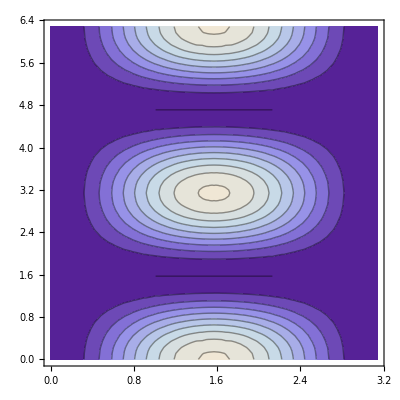

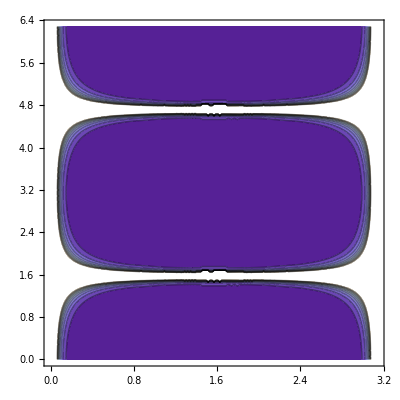

```mathematica
ContourPlot[Abs[1-Cos[Cos[ϕ]Sin[θ]]],{θ,0,π},{ϕ,0,2π}]
ContourPlot[Abs[1/(Exp[(1-Cos[Cos[ϕ]Sin[θ]])/0.01]-1)],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
Plot3D[Abs[1-Cos[Cos[ϕ]Sin[θ]]],{θ,0,π},{ϕ,0,2π}]
Plot3D[Abs[1/(Exp[(1-Cos[Cos[ϕ]Sin[θ]])/0.0000000000000001]-1)],{θ,0,π},{ϕ,0,2π},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
Limit[1/(Exp[(1-Cos[kx])/T]-1),kx->0,Assumptions->{T->0}]
```

DirectedInfinity[T]

```mathematica
Series[(-1+Exp[(1-Cos[kx])/(k T)])^-1,{kx,0,8}]/.{T->0.01,k->1}
```

0.02/kx^2-0.498333+4.16675 kx^2-0.347219 kx^4-173.6 kx^6+43.4026 kx^8+O[kx]^9

```mathematica
Limit[1/(Exp[(1-Cos[kx])/0]-1),kx->0]
Limit[1/(Exp[(1-Cos[0])/T]-1),T->0]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity